```mathematica
3
```

# A. Stromgren radius, decaying number density

## 0 - Constants

```mathematica
k =8.6173303*^-5; (*ev*)
solarLum = 2.38924969*^45;
solarMass  =2*^30;
a=3*^-13; (*/cm^3*)
(*conversion factor from parsec to cm*)
con = 3.08567758*^18; 
mP= 1.6726219*^-27;
planck = 6.62607004*^-34;
kmet = 1.38064852*^-23;
kcm  =1.38064852*^-16
alpha[T_] := 2.56*^-13/(T/1*^4)^0.83;
c = 299792458;
```

1.38065×10^-16

```mathematica
ScientificTicks[plot_Graphics,xSci_: False,ySci_: True]:=Module[{t},Show[plot,Ticks->{(t=Ticks/.AbsoluteOptions[plot,Ticks])[[1]]/.If[xSci,{x_,xlab_?NumericQ,r__}->{x,ScientificForm[x],r},{}],t[[2]]/.If[ySci,{y_,ylab_?NumericQ,r__}->{y,ScientificForm[y],r},{}]}]];

(*Reference https://www.physicsforums.com/threads/how-to-use-scientific-notation-in-a-graph-in-mathematica.315955/*)
```

```mathematica
25*^3*con
```

7.71419×10^22

## 1 - Stromgren for galaxy (constant n)

### 1.1 Basic

```mathematica
StandardForm[HoldForm[(3Q/(4*Pi*a*n^2))]^(1/3)+rSourceCm]
```

rSourceCm+((3 Q)/(4 π a n^2))^(1/3)

```mathematica
rStrom[luminosity_, temp_, rSource_, n_]:= Module[ {Q, rSourceCm}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con;
((3Q/(4*Pi*a*n^2))^(1/3)+rSourceCm)/con]
```

```mathematica
rStrom[2*^10, 1000000, 100000, 0.01] (*answer in pc *)
```

137624.

### 1.2 Temperature by galaxy mass

```mathematica
rStromM[luminosity_, M_, rSource_, n_]:= Module[ {Q, rSourceCm, aMod, T}, rSourceCm:= rSource*con;
T:= 0.59*mP*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100);
Q:= luminosity*solarLum/(2.82*T*k); 
(*aMod:= 4.13*^-13*(T/1*^4)^(-0.7131);*)
(*aMod:=1*^-13;*)
aMod = 2.56*^-13/(T/10^4)^-0.83;
{((3Q/(4*Pi*aMod*n^2))^(1/3)+rSourceCm)/con}]
```

```mathematica
rStromM[1.5*^10, 1*^12, 50000, 0.001]
```

```mathematica
urceCmce
```

{432587.}

```mathematica
rStromM[2*^10, 1*^12, 100000, 0.01]
```

## 2 - Exponential and Gaussian decay profiles

2.1 - Decay profiles, n goes to zero, takes temperature as input

### 2.1.1 Constant a

```mathematica
rExp[luminosity_, temp_, rSource_, beta_, n0_]:= Module[ {Q, rSourceCm}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con;
{(Q(3-2*beta)/(4*Pi*a*n0^2)+rSourceCm^(3-2beta))^(1/(3-2beta))/con}]
```

```mathematica
rGauss[luminosity_,temp_,rSource_,d_,n0_]:= Module[{Q, rSourceCm, dCm}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con; dCm :=d*con; {Solve[Q/(a*4*Pi*n0^2)==Integrate[r^2*Exp[-2r^2/d^2],{r,rSourceCm,rStrom}],rStrom]}]
```

```mathematica
rExp[1.5*^10, 1000000, 5*^4,1.2, 0.001]
```

{1.92421×10^117}

```mathematica
5.7*^25/con
```

1.84724×10^7

```mathematica
rGauss[2*^10,1000,1*^5,1.5*^24,0.01]
```

{{{rStrom→-9.43843×10^23}}}

### 2.1.2 Temperature dependent a

```mathematica
rExpa[luminosity_, temp_, rSource_, beta_, n0_]:= Module[ {Q, rSourceCm, aMod}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con;
aMod:= 4.13*^-13*(temp/10000)^(-0.7131); 
{(Q(3-2*beta)/(4*Pi*aMod*n0^2)+rSourceCm^(3-2beta))^(1/(3-2beta))/con, Q}]
```

```mathematica
rExpa[2*^10, 10000, 1*^5, 0.7, 0.001]
```

{9.99524×10^26,1.96639×10^55}

2.2 - Non-zero n profiles (constant added so n does not go to zero)

### Exponential

```mathematica
StandardForm[Q/(4*Pi*aMod)==n0^2/(3-2beta)(r^(3-2beta)-rSourceCm^(3-2beta))+2n0*nc*(r^(2-beta)-rSourceCm^(2-beta))+nc^2]
```

Q/(4 aMod π)==nc^2+(n0^2 (r^(3-2 beta)-rSourceCm^(3-2 beta)))/(3-2 beta)+2 n0 nc (r^(2-beta)-rSourceCm^(2-beta))

```mathematica
rExpaC[luminosity_, temp_, rSource_, beta_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con;
aMod:= 4.13*^-13*(temp/10000)^(-0.7131); 
(*(Solve[Q/(4*Pi*aMod)==n0^2/(3-2beta)(r^(3-2beta)-rSourceCm^(3-2beta))+2n0*nc*(r^(2-beta)-rSourceCm^(2-beta))+nc^2(r^2-rSourceCm^2),r])/con]*)
Solve[(Q*(3-2beta)/(4Pi aMod n0^2)+rSource^(3-2beta))^(1/(3-2beta)) == r, r]]
```

```mathematica
rExpaC[2*^10, 10000, 1*^5, 0.1, 0.001, 0.00001]
```

{{r→1.20391×10^26}}

```mathematica
1.38565*^41/con
```

4.49059×10^22

```mathematica
2.5*^26/con
```

8.10195×10^7

### Gaussian

```mathematica
rGaussaC[luminosity_, temp_, rSource_, d_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*con;
aMod:= 4.13*^-13*(temp/10000)^(-0.7131); 
{Solve[Q/(4*Pi*aMod)==Integrate[n0^2r^2Exp[-2r^2/d^2]+2n0*nc*r^2Exp[-r^2/d^2]+nc^2r^2, {r, rSourceCm, rStrom}], rStrom]}]
```

```mathematica
rGaussaC[2*^10,1000,1*^5,1.5*^24,0.01, 0.0001]
```

{{{rStrom→-5.21319×10^26-8.93179×10^26 ⅈ},{rStrom→-5.21319×10^26+8.93179×10^26 ⅈ},{rStrom→1.04264×10^27}}}

```mathematica
1.04246*^27/con
```

3.37838×10^8

2.3 - Non-zero n; temperature mass dependent

#### Exponential

```mathematica
StandardForm[Q/(4*Pi*aMod)==n0^2/(3-2beta)(r^(3-2beta)-rSourceCm^(3-2beta))+2n0*nc/(3-beta)(r^(3-beta)-rSourceCm^(3-beta))+nc^2*(r^3-rSourceCm^3)/3] 
(*equation 19 in the progress report draft*)
```

Q/(4 aMod π)==1/3 nc^2 (r^3-rSourceCm^3)+(n0^2 (r^(3-2 beta)-rSourceCm^(3-2 beta)))/(3-2 beta)+(2 n0 nc (r^(3-beta)-rSourceCm^(3-beta)))/(3-beta)

luminosity is in solar lum, M is in solar masses, rSource in pc, n0 and nc in cm^3. Outputs in cm

```mathematica
rExpaCT[luminosity_, M_, rSource_, beta_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod, T}, rSourceCm:= rSource*con;
T:= 0.59*mP*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100); (*equation 23*)
Q:= luminosity*solarLum/(2.82*T*k); 
(*aMod:= 4.13*^-13*(T/10000)^(-0.7131);*)
aMod = 2.56*^-13/(T/1*^4)^0.83;
{(Solve[Q/(4*Pi*aMod)==n0^2/(3-2beta)(r^(3-2beta)-rSourceCm^(3-2beta))+2n0*nc/(3-beta)(r^(3-beta)-rSourceCm^(3-beta))+nc^2*(r^3-rSourceCm^3)/3,r])}]
```

```mathematica
rExpaCT[1.5*^10, 1*^12, 2*^5, 1.2, 0.001, 0.00003]
```

{{{r→-6.9806×10^24-1.20908×10^25 ⅈ},{r→-6.9806×10^24+1.20908×10^25 ⅈ},{r→1.39612×10^25}}}

```mathematica
1.3*^25/con
```

4.21301×10^6

```mathematica
8*^24/con
```

2.59262×10^6

#### Gaussian

```mathematica
TraditionalForm[Q/(4*Pi*aMod)==HoldForm[Integrate[n0^2r^2Exp[-2r^2/d^2]+2n0*nc*r^2Exp[-r^2/d^2]+nc^2r^2, {r, rSourceCm, rStrom}]]]
(*equation 22 in the progress report draft*)
```

Q/(4 π aMod)==∫_rSourceCm^rStrom (n0^2 r^2 exp(-(2 r^2)/d^2)+2 n0 nc r^2 exp(-r^2/d^2)+nc^2 r^2)ⅆr

```mathematica
rGaussaCT[luminosity_, M_, rSource_, d_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod, T}, rSourceCm:= rSource*con;
T:= 0.59*mP*6.67408*^-11
*M*solarMass/(2*1.38064852*^-23*rSourceCm/100);
Q:= luminosity*solarLum/(2.82*T*k); 
(*aMod:= 4.13*^-13*(T/10000)^(-0.7131);*)
aMod = 2.56*^-13/(T/10^4)^0.83;
{Solve[Q/(4*Pi*aMod)==Integrate[n0^2r^2Exp[-2r^2/d^2]+2n0*nc*r^2Exp[-r^2/d^2]+nc^2r^2, {r, rSourceCm, rStrom}], rStrom]}]
```

```mathematica
rGaussaCT[1.5*^10,1*^12,5*^4,7.71419395*^22,0.001, 0.0001]
```

{{{rStrom→-5.91768×10^24-1.02192×10^25 ⅈ},{rStrom→-5.91768×10^24+1.02192×10^25 ⅈ},{rStrom→1.18354×10^25}}}

```mathematica
(1.110166*^25/con)
```

3.5978×10^6

## 3 -Plots

### 3.1 Size of Stromgren spheres

```mathematica
Graphics[{Opacity[0.5], Black,Disk[{0,0},100], Blue,Disk[{0,0},476.244],Opacity[0.1] ,Disk[{0,0},5.182053652856198*^27/con/1000], Disk[{0,0},6.499840726198163*^27/con/1000]}]
```

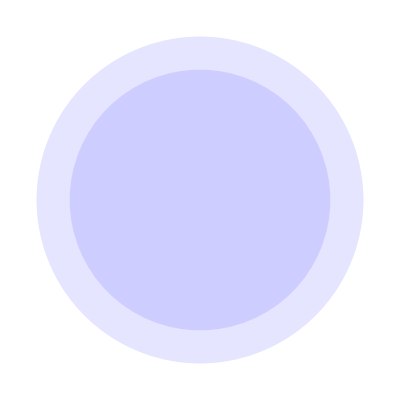

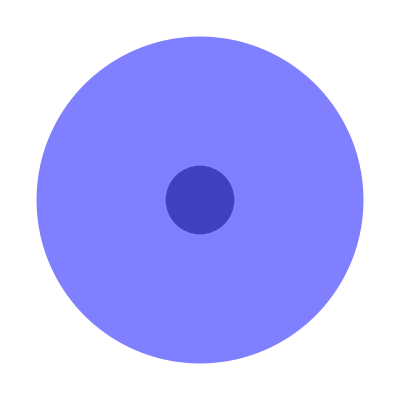

```mathematica
Graphics[{Opacity[0.5], Black,Disk[{0,0},100], Blue,Disk[{0,0},476.244]}]
```

### 3.2 - Parameter sensitivity

#### 3.2.1 Beta sensitivity for exponential

```mathematica
params = {0,0.1,0.2,0.4,0.5,0.6, 0.8, 0.9, 1, 1.2, 1.4,1.8, 1000};
```

```mathematica
Cases[Flatten[r/.rExpaCT[1.5*^10, 1*^12, 5*^4, #, 0.001, 0.00003]&/@params], s_/; Im[s] ==0&&s>0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{1.15842×10^24,1.1422×10^25,1.22246×10^25,1.22274×10^25,1.22274×10^25,1.22274×10^25,1.22274×10^25,1.22274×10^25,1.22274×10^25,1.22274×10^25,1.22274×10^25,1.22274×10^25,1.22274×10^25}

```mathematica
temp = Cases[Flatten[r/.rExpaCT[1.5*^10, 1*^12, 5*^4, #, 0.001, 0.00003]&/@params], s_/; Im[s] ==0&&s>0];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ListPlot[Transpose[{params, temp}]]
```

-Graphics-

#### 3.2.2. d sensitivity Gaussian

```mathematica
dVals = {1*^16, 1*^20, 1*^21, 1*^22, 1*^23, 1*^24, 1*^26} ;
```

```mathematica
temp2 = Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1*^12,5*^4,#,0.001, 0.00003]&/@dVals], s_/;Im[s]==0&&s>0]
```

{1.22274×10^25,1.22274×10^25,1.22274×10^25,1.22299×10^25,1.24831×10^25,3.14885×10^25,3.05505×10^27}

```mathematica
ListPlot[Transpose[{dVals, temp2}]]
```

Transpose::nmtx: The first two levels of {{100000,10000000000,100000000000000000000,1000000000000000000000,10000000000000000000000,100000000000000000000000,1000000000000000000000000,10000000000000000000000000,100000000000000000000000000,1000000000000000000000000000,1000000000000000000000000000000},{1.22274×10^25,1.22274×10^25,1.22299×10^25,1.24831×10^25,3.14885×10^25,3.05515×10^26,3.05505×10^27,3.05505×10^28,3.05505×10^31}} cannot be transposed.

Transpose::nmtx: The first two levels of {{100000.,1.×10^10,1.×10^20,1.×10^21,1.×10^22,1.×10^23,1.×10^24,1.×10^25,1.×10^26,1.×10^27,1.×10^30},{1.22274×10^25,1.22274×10^25,1.22299×10^25,1.24831×10^25,3.14885×10^25,3.05515×10^26,3.05505×10^27,3.05505×10^28,3.05505×10^31}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{100000.,1.×10^10,1.×10^20,1.×10^21,1.×10^22,1.×10^23,1.×10^24,1.×10^25,1.×10^26,1.×10^27,1.×10^30},{1.22274×10^25,1.22274×10^25,1.22299×10^25,1.24831×10^25,3.14885×10^25,3.05515×10^26,3.05505×10^27,3.05505×10^28,3.05505×10^31}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{100000,10000000000,100000000000000000000,1000000000000000000000,10000000000000000000000,100000000000000000000000,1000000000000000000000000,10000000000000000000000000,100000000000000000000000000,1000000000000000000000000000,1000000000000000000000000000000},{1.22274×10^25,1.22274×10^25,1.22299×10^25,1.24831×10^25,3.14885×10^25,3.05515×10^26,3.05505×10^27,3.05505×10^28,3.05505×10^31}}]]

### Temperature dependencies

```mathematica
rExpT[luminosity_, T_, rSource_, beta_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod}, rSourceCm:= rSource*con;
(*T:= 0.59*mP*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100); (*equation 23*)*)
Q:= luminosity*solarLum/(2.82*T*k); 
(*aMod:= 4.13*^-13*(T/10000)^(-0.7131);*)
aMod :=2.56*^-13/(T/1*^4)^(0.833);
{(Solve[Q/(4*Pi*aMod)==n0^2/(3-2beta)(r^(3-2beta)-rSourceCm^(3-2beta))+2n0*nc/(3-beta)(r^(3-beta)-rSourceCm^(3-beta))+nc^2*(r^3-rSourceCm^3)/3,r])}]
```

```mathematica
rGaussT[luminosity_, T_, rSource_, d_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod}, rSourceCm:= rSource*con;
(*T:= 0.59*mP*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100);*)
Q:= luminosity*solarLum/(2.82*T*k); 
(*aMod:= 4.13*^-13*(T/10000)^(-0.7131);*)
aMod = 2.56*^-13/(T/1*^4)^0.83;
{Solve[Q/(4*Pi*aMod)==Integrate[n0^2r^2Exp[-2r^2/d^2]+2n0*nc*r^2Exp[-r^2/d^2]+nc^2r^2, {r, rSourceCm, rStrom}], rStrom]}]
```

```mathematica
rGaussT[1.5*^10,10000000,2*^5,6*^23,0.001, 0.00003]
```

{{{rStrom→-1.81874×10^25},{rStrom→-2.82602×10^23},{rStrom→1.847×10^25}}}

```mathematica
rStromT[luminosity_, T_, rSource_, n_]:= Module[ {Q, rSourceCm, aMod}, rSourceCm:= rSource*con;
Q:= luminosity*solarLum/(2.82*T*k); 
(*aMod:= 4.13*^-13*(T/1*^4)^(-0.7131);*)
aMod = 2.56*^-13/(T/1*^4)^0.83;
{((3Q/(4*Pi*aMod*n^2))^(1/3)+rSourceCm)/con}]
```

```mathematica
rExp
```

```mathematica
rGaussT[1.5*^10,1*^6,5*^4,7.71419395*^22,0.001, 0.00003]
```

{{{rStrom→-6.87883×10^24-1.16791×10^25 ⅈ},{rStrom→-6.87883×10^24+1.16791×10^25 ⅈ},{rStrom→1.37577×10^25}}}

```mathematica
rExpT[1.5*^10, 1*^6, 5*^4, 1.2, 0.001, 0.0003]
```

{{{r→-1.66768×10^23-2.8885×10^23 ⅈ},{r→-1.66768×10^23+2.8885×10^23 ⅈ},{r→3.33535×10^23}}}

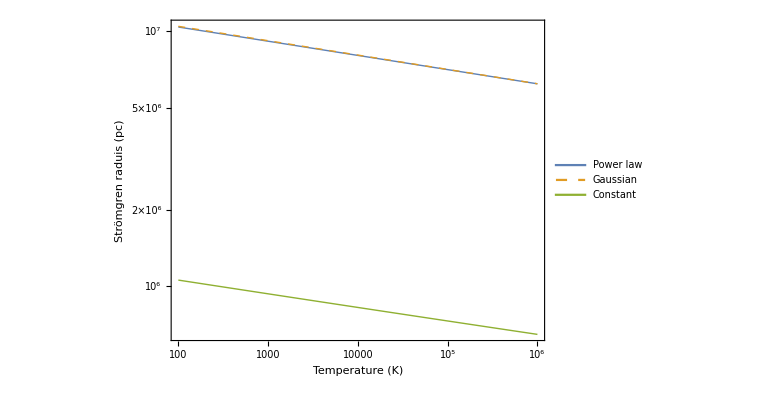

```mathematica
t= LogLogPlot[{Cases[Flatten[r/.rExpT[1.5*^10, x, 5*^4, 1.2, 0.001, 0.00003]], s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussT[1.5*^10,x,5*^4,7.71419395*^22,0.001, 0.00003]], s_/;Im[s]==0&&s>0]/con , rStromT[1.5*^10, x, 50000, 0.001]}, {x, 100,1000000}, PlotLegends->Placed[
{"Power law", "Gaussian", "Constant"},{0.2,0.5}], AxesLabel->{"Stromgren radius (Pc)", "Temperature (K)"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Directive[Thick], Directive[Thick, Dashed],Thick}, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style["Strömgren raduis (pc)",18,FontFamily->"Arial"],None},{Style["Temperature (K)",18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]
```

```mathematica
3t
```

```mathematica
Export["TplotFinal3.png",t]
```

TplotFinal3.png

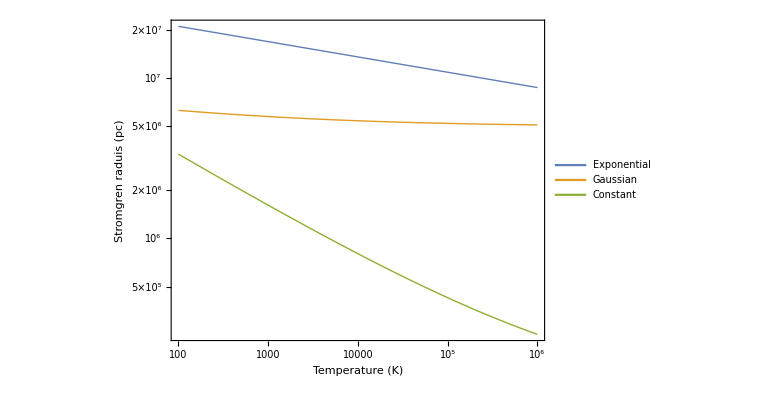
```mathematica
-Graphics-
Export["testMplot.png",t]
```

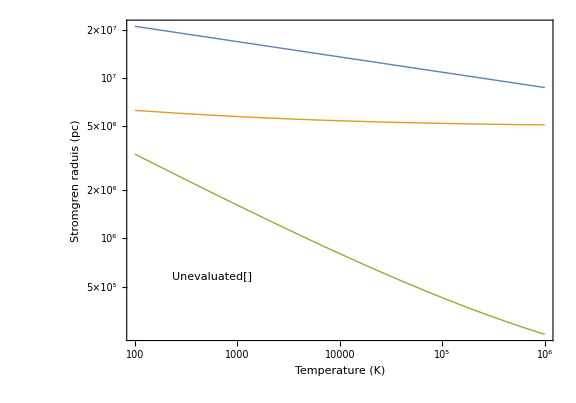

testMplot.png

### Radius by initial number density

```mathematica
1.3*^10, 1*^12, 1*^5, 1, 0.001, 0.00001]
```

```mathematica
rGaussaCT[1.5*^10,1*^12,5*^4,7.71419395*^22,0.001, 0.00003]
rGaussaCT[1.5*^10,1*^12,5*^4,7.71419395*^22,0.001, 0.00003]
Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1*^12,5*^4,1.71419395*^25,0.001, 0.00003]], s_/;Im[s]==0&&s>0]/con
```

{{{rStrom→-6.1897×10^24-1.04586×10^25 ⅈ},{rStrom→-6.1897×10^24+1.04586×10^25 ⅈ},{rStrom→1.23794×10^25}}}

{{{rStrom→-6.1897×10^24-1.04586×10^25 ⅈ},{rStrom→-6.1897×10^24+1.04586×10^25 ⅈ},{rStrom→1.23794×10^25}}}

{1.69719×10^8}

```mathematica
rGaussT[1.5*^10,3.092*^6,5*^4,7.71419395*^22,0.001, 0.00003]
```

{{{rStrom→-6.1897×10^24-1.04586×10^25 ⅈ},{rStrom→-6.1897×10^24+1.04586×10^25 ⅈ},{rStrom→1.23794×10^25}},3.092×10^6}

```mathematica
1.23794*^25/con
1.22274*^25/con
```

4.01189×10^6

3.96263×10^6

```mathematica
rExpaCT[1.5*^10, 1*^12, 5*^4, 1.2, 0.001, 0.00003]
```

```mathematica
rExpaCT[1.5*^10, 1*^12, 5*^4, 1.2, 0.001, 0.00003]
```

{{{r→-6.1137×10^24-1.05892×10^25 ⅈ},{r→-6.1137×10^24+1.05892×10^25 ⅈ},{r→1.22274×10^25}},3.09199×10^6}

```mathematica
u = LogLogPlot[{Cases[Flatten[r/.rExpaCT[1.5*^10, 1.5*^12, 2*^5, 1.2, n, 0.00005]], s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1.5*^12,2*^5,3*^23,n, 0.00005]], s_/;Im[s]==0&&s>0]/con, rStromT[1.5*^10, 1000000, 200000, n] }, {n, 0.00001,1},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style["Strömgren raduis (pc)",18,FontFamily->"Arial"],None},{Style[HoldForm["Initial number density ("  Superscript["cm", -3] ")"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]
```

ReplaceAll::reps: {rExpaCT[1.5×10^10,1.5×10^12,200000,1.2,0.0000100024,0.00005]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rExpaCT[1.5×10^10,1.5×10^12,200000,1.2,0.0000126515,0.00005]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rExpaCT[1.5×10^10,1.5×10^12,200000,1.2,0.0000160024,0.00005]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

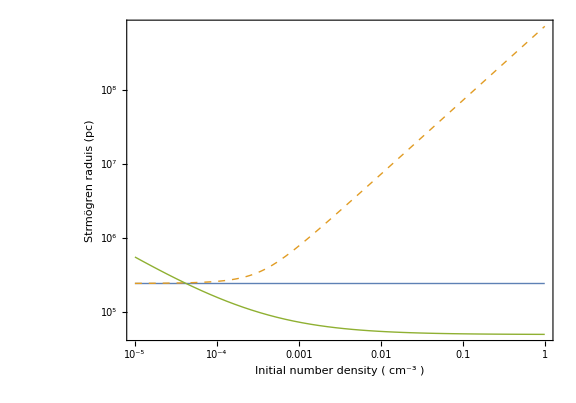

```mathematica
u = LogLogPlot[{Cases[Flatten[r/.rExpaCT[1.5*^10, 1*^12, 5*^4, 1.2, n, 0.00003]], s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1*^12,5*^4,7.71419395*^22,n, 0.00003]], s_/;Im[s]==0&&s>0]/con, rStromM[1.5*^10, 1*^12, 5*^4, n] }, {n, 0.00001,1},  AxesLabel->{ HoldForm["Initial number density"  (cm^3)], "Stromgren radius (Pc)"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Thick, Directive[Dashed, Thick], Thick}, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style["Strmögren raduis (pc)",18,FontFamily->"Arial"],None},{Style[HoldForm["Initial number density ("  Superscript["cm", -3] ")"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]
```

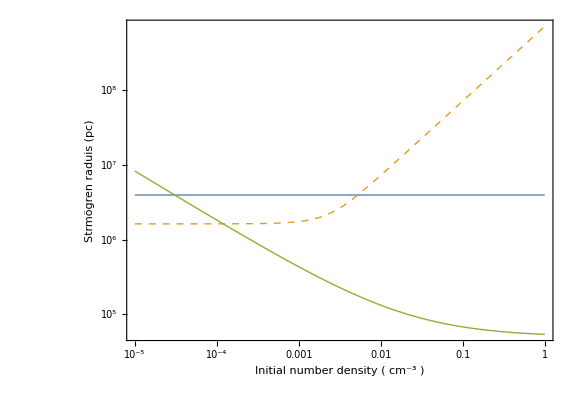

```mathematica
Export["nPlotFinal2.png",u]
```

nPlotFinal2.png

# B. Thomson scattering

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

### 0 - Constants

```mathematica
(*cross section photon electron in cm^2 *)
sigmaT = 8*^4Pi(ElectronCharge^2/(4Pi VacuumPermittivity*ElectronMass*SpeedOfLight^2))^2/3
```

(6.65246×10^-25 Coulomb^4 Second^2 Volt^2)/(Ampere^2 Kilogram^2 Meter^2)

### 1 - Constant n

```mathematica
luminosity_, M_, rSource_, n_
```

```mathematica
rStromM[1.5*^10, 1*^12, 2*^4, 0.001]
```

{370489.}

```mathematica
ThomCon[rStrom_, rSource_, n0_]:= sigmaT*n0*(rStrom-rSource)*con
```

```mathematica
ThomCon[3*^5, 2*^4, 0.001]
```

(12316.4 Coulomb^4 Second^2 Volt^2)/(Ampere^2 Kilogram^2 Meter^2)

### 2 - Exponential n

```mathematica
ThomExp[rStrom_, rSource_,beta_, n0_, nc_]:= Module[{rSourceCm, rStromCm},rSourceCm = rSource*con; 
rStromCm = rStrom*con; 
sigmaT(n0(rStromCm^(1-beta)-rSourceCm^(1-beta))/(1-beta) +nc(rStromCm-rSourceCm))]
```

```mathematica
ThomExp[1*^6, 5*^4, 1.2, 0.001, 0.00003]
```

(0.0000585029 Coulomb^4 Second^2 Volt^2)/(Ampere^2 Kilogram^2 Meter^2)

### 3 - Gaussian n

```mathematica
ThomGauss[rStrom_, rSource_, d_, n0_, nc_]:=Module[{rSourceCm, rStromCm}, rSourceCm = rSource*con; rStromCm=rStrom*con; 
Solve[tau == sigmaT*Integrate[n0*Exp[-r^2/d^2]+nc, {r,rSourceCm, rStromCm}], tau]]
```

```mathematica
ThomGauss[1*^6, 5*^4, 7.71419395*^22, 0.001, 0.00003]
```

{{tau→(0.0000587157 Coulomb^4 Second^2 Volt^2)/(Ampere^2 Kilogram^2 Meter^2)}}

```mathematica
LogLogPlot[{Cases[Flatten[r/.rExpaCT[1.5*^10, 1.5*^12, 2*^5, 1.2, n, 0.00005]], s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1.5*^12,2*^5,3*^23,n, 0.00005]], s_/;Im[s]==0&&s>0]/con, rStromT[1.5*^10, 1000000, 200000, n] }, {n, 0.00001,1}]
```

ReplaceAll::reps: {rExpaCT[1.5×10^10,1.5×10^12,200000,1.2,0.0000100024,0.00005]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rExpaCT[1.5×10^10,1.5×10^12,200000,1.2,0.0000126515,0.00005]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rExpaCT[1.5×10^10,1.5×10^12,200000,1.2,0.0000160024,0.00005]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Import["https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"]
```

```mathematica
testCell=Cell[BoxData[MakeBoxes[  LogLogPlot[{Cases[Flatten[r/.rExpaCT[1.5*^10, 1*^12, 5*^4, 1.2, n, 0.00003]], s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1*^12,5*^4,7.71419395*^22,n, 0.00003]], s_/;Im[s]==0&&s>0]/con, rStromM[1.5*^10, 1*^12, 5*^4, n] }, {n, 0.00001,1},  LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Thick, Directive[Dashed, Thick], Thick}, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style["Strmogren raduis (pc)",18,FontFamily->"Arial"],None},{Style[HoldForm["Initial number density ("  Superscript["cm", -3] ")"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]] ],"Input"];
testCell//CellPrint
CellToTeX[testCell]
```

```mathematica
LogLogPlot[{Cases[Flatten[r/.rExpaCT[1.5*^10,1000000000000,50000,1.2,n,0.00003]],s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1000000000000,50000,7.71419395*^22,n,0.00003]],s_/;Im[s]==0&&s>0]/con,rStromM[1.5*^10,1000000000000,50000,n]},{n,0.00001,1},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Thick,Directive[Dashed,Thick],Thick},ImageSize->Large,Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]],FrameLabel->{{"Strmogren raduis (pc)",None},{"Initial number density (" ("cm")^-3 ")",None}},AspectRatio->0.7,ImageSize->600]
```

```mathematica
LogLogPlot[{Cases[Flatten[r/.rExpaCT[1.5*^10,1000000000000,50000,1.2,n,0.00003]],s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1000000000000,50000,7.71419395*^22,n,0.00003]],s_/;Im[s]==0&&s>0]/con,rStromM[1.5*^10,1000000000000,50000,n]},{n,0.00001,1},AxesLabel->{"Initial number density" cm^3,"Stromgren radius (Pc)"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Thick,Directive[Dashed,Thick],Thick},ImageSize->Large,Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]],FrameLabel->{{"Strmögren raduis (pc)",None},{"Initial number density (" ("cm")^-3 ")",None}},AspectRatio->0.7,ImageSize->600]
```

```mathematica
LogLogPlot[{Cases[Flatten[r/.rExpaCT[1.5*^10,1000000000000,50000,1.2,n,0.00003]],s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1000000000000,50000,7.71419395*^22,n,0.00003]],s_/;Im[s]==0&&s>0]/con,rStromM[1.5*^10,1000000000000,50000,n]},{n,0.00001,1}]
```

```mathematica
LogLogPlot[{Cases[Flatten[r/.rExpaCT[1.5*^10,1000000000000,50000,1.2,n,0.00003]],s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussaCT[1.5*^10,1000000000000,50000,7.71419395*^22,n,0.00003]],s_/;Im[s]==0&&s>0]/con,rStromM[1.5*^10,1000000000000,50000,n]},{n,0.00001,1}]
```

```mathematica
LogLogPlot[{Cases[Flatten[r/.rExpT[1.5*^10,x,50000,1.2,0.001,0.0003]],s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussT[1.5*^10,x,50000,7.71419395*^22,0.001,0.0003]],s_/;Im[s]==0&&s>0]/con,rStromT[1.5*^10,x,50000,0.001]},{x,100,1000000}]
```

```mathematica
LogLogPlot[{Cases[Flatten[r/.rExpT[1.5*^10,x,50000,1.2,0.001,0.0003]],s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussT[1.5*^10,x,50000,7.71419395*^22,0.001,0.0003]],s_/;Im[s]==0&&s>0]/con,rStromT[1.5*^10,x,50000,0.001]},{x,100,1000000}]
```

```mathematica
LogLogPlot[{Cases[Flatten[r/.rExpT[1.5*^10,x,50000,1.2,0.001,0.0003]],s_/;Im[s]==0&&s>0]/con,Cases[Flatten[rStrom/.rGaussT[1.5*^10,x,50000,7.71419395*^22,0.001,0.0003]],s_/;Im[s]==0&&s>0]/con,rStromT[1.5*^10,x,50000,0.001]},{x,100,1000000}]
```

\begin{mmaCell}[morefunctionlocal={x},morepattern={s_, s},moredefined={con}]{Input}
  LogLogPlot[\{\mmaFrac{Cases[Flatten[r/.\(\pmb{\,}\)rExpT[1.5`*^10,x,50000,1.2`,0.001`,0.0003`]],s_/;Im[s]==0&&s>0]}{con},\mmaFrac{Cases[Flatten[rStrom/.\(\pmb{\,}\)rGaussT[1.5`*^10,x,50000,7.71419395`*^22,0.001`,0.0003`]],s_/;Im[s]==0&&s>0]}{con},rStromT[1.5`*^10,x,50000,0.001`]\},\{x,100,1000000\}]
\end{mmaCell}

```mathematica
$CellContext`r$CellContext`rStrom1.5e10
```

MakeBoxes::boxfmt: SyntaxAnnotations`Private`parse[Main][FontSize→10] in MakeBoxes[SyntaxAnnotations`Private`parse[Main][LogLogPlot[{Cases[Flatten[ReplaceAll[«2»]],Pattern[«2»]/;And[«2»]]/con,Cases[Flatten[ReplaceAll[«2»]],Pattern[«2»]/;And[«2»]]/con,rStromT[1.5×10^10,x,50000,0.001]},{x,100,1000000}]],SyntaxAnnotations`Private`parse[Main][FontSize→10]] is not a box formatting type. A box formatting type is any member of $BoxForms.

CellsToTeXException::unsupported: Box: MakeBoxes[LogLogPlot[{Cases[Flatten[r/.rExpT[«6»]],s_/;Equal[«2»]&&Greater[«2»]]/con,Cases[Flatten[rStrom/.rGaussT[«6»]],s_/;Equal[«2»]&&Greater[«2»]]/con,rStromT[1.5×10^10,x,50000,0.001]},{x,100,1000000}],FontSize→10] is not one of supported: {CellsToTeX`Configuration`syntaxBox[_,DefinedSymbol,___],CellsToTeX`Configuration`syntaxBox[_,UndefinedSymbol,___],CellsToTeX`Configuration`syntaxBox[_,LocalVariable,___],CellsToTeX`Configuration`syntaxBox[_,FunctionLocalVariable,___],CellsToTeX`Configuration`syntaxBox[_,PatternVariable,___],CellsToTeX`Configuration`syntaxBox[_,LocalScopeConflict,___],«23»,HoldPattern[UnderoverscriptBox[Repeated[_,{3}],OptionsPattern[]]],HoldPattern[FractionBox[Repeated[_,{2}],OptionsPattern[]]],HoldPattern[SqrtBox[Repeated[_,{1}],OptionsPattern[]]],HoldPattern[RadicalBox[Repeated[_,{2}],OptionsPattern[]]],_String}. Exception occurred in CellsToTeX`Configuration`boxesToTeXProcessor[{BoxRules→{CellsToTeX`Configuration`syntaxBox[CellsToTeX`Private`boxes$_,DefinedSymbol,___]:>\mmaDef{<>CellsToTeX`Configuration`makeString[CellsToTeX`Private`boxes$]<>},CellsToTeX`Configuration`syntaxBox[CellsToTeX`Private`boxes$_,UndefinedSymbol,___]:>\mmaUnd{<>CellsToTeX`Configuration`makeString[CellsToTeX`Private`boxes$]<>},«31»,CellsToTeX`Private`str$_String:>StringReplace[CellsToTeX`Configuration`makeStringDefault[CellsToTeX`Private`str$],{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],RuleDelayed[«2»]}]},StringRules→{<|→<|,«6»,«1»},{«1»}}].

Failure[…]

CellsToTeXException::missingCellStyle: Couldn't extract cell style from given boxes. Either use "Style" option or provide Cell expression with defined style. Given boxes are: Cell[BoxData[RowBox[{LogLogPlot,[,RowBox[{RowBox[{«3»}],,,RowBox[{«3»}]}],]}]],FontSize→10,Input]. Exception occurred in CellToTeX[Cell[BoxData[RowBox[{LogLogPlot,[,RowBox[{RowBox[«1»],,,RowBox[«1»]}],]}]],FontSize→10,Input]].

Failure[…]

CellsToTeXException::missingCellStyle: Couldn't extract cell style from given boxes. Either use "Style" option or provide Cell expression with defined style. Given boxes are: Cell[BoxData[RowBox[{LogLogPlot,[,RowBox[{RowBox[{«3»}],,,RowBox[{«3»}]}],]}]],FontSize→10,Input]. Exception occurred in CellToTeX[Cell[BoxData[RowBox[{LogLogPlot,[,RowBox[{RowBox[«1»],,,RowBox[«1»]}],]}]],FontSize→10,Input]].

Failure[…]

\begin{mmaCell}[morefunctionlocal={n},morepattern={s_, s},moredefined={con, rStromM}]{Input}
  LogLogPlot[\{\mmaFrac{Cases[Flatten[r/.\(\pmb{\,}\)rExpaCT[1.5`*^10,1000000000000,50000,1.2`,n,0.00003`]],s_/;Im[s]==0&&s>0]}{con},\mmaFrac{Cases[Flatten[rStrom/.\(\pmb{\,}\)rGaussaCT[1.5`*^10,1000000000000,50000,7.71419395`*^22,n,0.00003`]],s_/;Im[s]==0&&s>0]}{con},rStromM[1.5`*^10,1000000000000,50000,n]\},\{n,0.00001`,1\}]
\end{mmaCell}

\begin{mmaCell}[morefunctionlocal={n},morepattern={s_, s},moredefined={con, rStromM}]{Input}
  LogLogPlot[\{\mmaFrac{Cases[Flatten[r/.\(\pmb{\,}\)rExpaCT[1.5`*^10,1000000000000,50000,1.2`,n,0.00003`]],s_/;Im[s]==0&&s>0]}{con},\mmaFrac{Cases[Flatten[rStrom/.\(\pmb{\,}\)rGaussaCT[1.5`*^10,1000000000000,50000,7.71419395`*^22,n,0.00003`]],s_/;Im[s]==0&&s>0]}{con},rStromM[1.5`*^10,1000000000000,50000,n]\},\{n,0.00001`,1\},AxesLabel\(\pmb{\to}\)\{"Initial number density" \mmaSup{cm}{3},"Stromgren radius (Pc)"\},LabelStyle\(\pmb{\to}\)Directive[FontFamily\(\pmb{\to}\)"Arial",Black,FontSize\(\pmb{\to}\)18],PlotStyle\(\pmb{\to}\)\{Thick,Directive[Dashed,Thick],Thick\},ImageSize\(\pmb{\to}\)Large,Frame\(\pmb{\to}\)True,Axes\(\pmb{\to}\)False,FrameStyle\(\pmb{\to}\)Directive[Thickness[0.003`],Black,18],FrameTicksStyle\(\pmb{\to}\)Directive[Thickness[0.004`]],FrameLabel\(\pmb{\to}\)\{\{"Strm\pmb{{\"o}}gren raduis (pc)",None\},\{"Initial number density (" \mmaSup{"cm"}{-3} ")",None\}\},AspectRatio\(\pmb{\to}\)0.7`,ImageSize\(\pmb{\to}\)600]
\end{mmaCell}

\begin{mmaCell}[morefunctionlocal={n},morepattern={s_, s},moredefined={con, rStromM}]{Input}
  LogLogPlot[\{\mmaFrac{Cases[Flatten[r/.\(\pmb{\,}\)rExpaCT[1.5`*^10,1000000000000,50000,1.2`,n,0.00003`]],s_/;Im[s]==0&&s>0]}{con},\mmaFrac{Cases[Flatten[rStrom/.\(\pmb{\,}\)rGaussaCT[1.5`*^10,1000000000000,50000,7.71419395`*^22,n,0.00003`]],s_/;Im[s]==0&&s>0]}{con},rStromM[1.5`*^10,1000000000000,50000,n]\},\{n,0.00001`,1\},LabelStyle\(\pmb{\to}\)Directive[FontFamily\(\pmb{\to}\)"Arial",Black,FontSize\(\pmb{\to}\)18],PlotStyle\(\pmb{\to}\)\{Thick,Directive[Dashed,Thick],Thick\},ImageSize\(\pmb{\to}\)Large,Frame\(\pmb{\to}\)True,Axes\(\pmb{\to}\)False,FrameStyle\(\pmb{\to}\)Directive[Thickness[0.003`],Black,18],FrameTicksStyle\(\pmb{\to}\)Directive[Thickness[0.004`]],FrameLabel\(\pmb{\to}\)\{\{"Strmogren raduis (pc)",None\},\{"Initial number density (" \mmaSup{"cm"}{-3} ")",None\}\},AspectRatio\(\pmb{\to}\)0.7`,ImageSize\(\pmb{\to}\)600]
\end{mmaCell}

# 4 - Stromgren radii local group

```mathematica
rMW = Cases[Flatten[r/.rExpaCT[1.5*^10, 1*^12, 5*^4, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{1251.98}

```mathematica
rM31= Cases[Flatten[r/.rExpaCT[2.6*^10, 1*^12, 1*^5, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{1564.27}

```mathematica
rM33 = Cases[Flatten[r/.rExpaCT[7.5*^8, 5*^10, 1*^4, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{498.92}

```mathematica
colorz={{Red,Opacity[0.3]},{Blue,Opacity[0.3]},{Green,Opacity[0.3]}};
```

```mathematica
spheres = Graphics3D[{Opacity[0.3], Red, Sphere[{0,0,0}, rMW],Black, Sphere[{0,0,0}, 50],  Blue, Sphere[{-800, 0, 0}, rM31], Black, Sphere[{-800, 0, 0}, 100], Green, Sphere[{-840, 0, -230}, rM33], Black, Sphere[{-840, 0, -230}, 10]}, Axes->True , AxesLabel->{"kpc", "", ""},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16],ImageSize->600];
Legended[Show[spheres],SwatchLegend[{colorz[[1]],colorz[[2]],Green},Style[#,18,FontFamily->"Arial"]&/@{"Milky Way","Andromeda","Triangulum"}]]
```

-Graphics3D-

```mathematica
rM82 =  Cases[Flatten[r/.rExpaCT[7.5*^10, 1*^12, 13*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{1283.39}

```mathematica
rLMC= Cases[Flatten[r/.rExpaCT[1*^9, 1*^9, 2*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{625.666}

```mathematica
rSagit= Cases[Flatten[r/.rExpaCT[2*^7, 1*^7, 1.1*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{213.128}

```mathematica
rSMC= Cases[Flatten[r/.rExpaCT[4*^9, 1*^7, 1*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{1239.66}

```mathematica
rBootes= Cases[Flatten[r/.rExpaCT[2*^4, 1*^7, 0.5*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{20.3816}

```mathematica
rSculptor= Cases[Flatten[r/.rExpaCT[2*^6, 1*^7, 0.4*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{93.4137}

```mathematica
rDraco= Cases[Flatten[r/.rExpaCT[3*^5, 1*^7, 0.35*^3, 1.2, 0.001, 0.0003]], s_/;Im[s]==0&&s>0]/con/1000
```

{49.2593}

```mathematica
colorz={{Red,Opacity[0.3]},{Blue,Opacity[0.3]},{Green,Opacity[0.3]},{Purple,Opacity[0.3]},{Orange,Opacity[0.3]},{Pink,Opacity[0.3]},{Gray,Opacity[0.3]}};
```

```mathematica
spheres = Graphics3D[{Opacity[0.3], Red, Sphere[{0,0,0}, rMW],Black, Sphere[{0,0,0}, 50],  Blue, Sphere[{-10, 20, 5}, rLMC], Black, Sphere[{-10, 20, 5}, 4], Green, Sphere[{2, 0, -5}, rSagit], Black, Sphere[{2, 0, -5}, 1.3], Purple, Sphere[{-8, 30, 5}, rSMC], Black, Sphere[{-8, 30, 5}, 1],Orange, Sphere[{0, -5, 40}, rBootes], Black, Sphere[{0, -5, 40}, 0.5], Pink, Sphere[{-3, 50, -10}, rSculptor], Black, Sphere[{-3, 50, -10}, 0.4], Gray, Sphere[{10, 0, 40}, rDraco], Black, Sphere[{10, 0, 40}, 0.35]}, Axes->True , AxesLabel->{"kpc", "", ""},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16]];
Legended[Show[spheres],SwatchLegend[{colorz[[1]],colorz[[2]],Green},Style[#,18,FontFamily->"Arial"]&/@{"Milky Way","Andromeda","Triangulum"}]]
```

-Graphics3D-

```mathematica
spheres = Graphics3D[{Opacity[0.3], Red, Sphere[{0,0,0}, rMW],Black, Sphere[{0,0,0}, 50],  Blue, Sphere[{-10, 20, 5}, rLMC], Black, Sphere[{-10, 20, 5}, 4], Green, Sphere[{2, 0, -5}, rSagit], Black, Sphere[{2, 0, -5}, 1.3], Yellow, Sphere[{-8, 30, 5}, rSMC], Black, Sphere[{-8, 30, 5}, 1]}, Axes->True , AxesLabel->{"kpc", "", ""}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16], ImageSize->600];
Legended[Show[spheres],SwatchLegend[{colorz[[1]],colorz[[2]],Green, Yellow},Style[#,18,FontFamily->"Arial"]&/@{"Milky Way","Large Magellanic Cloud","Sagittarius","Small Magellanic Cloud"}]]
```

-Graphics3D-

```mathematica
spheres = Graphics3D[{Opacity[0.3], Black, Sphere[{0,0,0}, 50], Orange, Sphere[{0, -5, 40}, rBootes], Black, Sphere[{0, -5, 40}, 0.5], Pink, Sphere[{-3, 50, -10}, rSculptor], Black, Sphere[{-3, 50, -10}, 0.4], Green, Sphere[{10, 0, 40}, rDraco], Black, Sphere[{10, 0, 40}, 0.35]}, Axes->True , AxesLabel->{"kpc", "", ""},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16],ImageSize->600];
Legended[Show[spheres],SwatchLegend[{Orange,Pink,Green},Style[#,18,FontFamily->"Arial"]&/@{"Bootes III","Sculptor","Draco"}]]
```

-Graphics3D-

```mathematica
Legended[Show[spheres],SwatchLegend[{colorz[[1]],colorz[[2]],Green},{"Milky Way","Andromeda","Triangulum"}]]
```

```mathematica
Legended[Show[spheres],SwatchLegend[{colorz[[1]],colorz[[4]],colorz[[2]]},{"Milky Way","Small Magellanic Cloud","Large Magellanic Cloud"}]]
```

# Mass

```mathematica
1.38064852*^-23*1*^6*rMW*3.086*^16*1.2/(1000*0.59*mP*6.67408*^-11)
```

{6.62773×10^36}

## Plot local cluster

```mathematica
rExpaCT[1.5*^10, 1*^12, 2*^5, 1.2, 0.001, 0.00003]
```

{{{r→-6.9806×10^24-1.20908×10^25 ⅈ},{r→-6.9806×10^24+1.20908×10^25 ⅈ},{r→1.39612×10^25}}}

```mathematica
1.5/20
```

0.075

# Intensity

```mathematica
intensity[n0_,nc_, d_, rStrom_] := 5.4*^-39*Integrate[(n0(d*Sec[theta])^-2.4+nc)^2d Sec[theta]^2, {theta, 0, ArcCos[d/(rStrom*10^3*con)]}]/Sqrt[1*^7]
```

```mathematica
corrFac[pixelWidth_, pixelHeight_, radius_]:= Module[{width, height, correction, gridElements,d, dCm, intensities}, 
width:= radius*2/(Sqrt[2]*(pixelWidth -1)); 
height:= width;
correction:= 4*Pi*width*height;
gridElements:= Tuples[{Range[1,pixelWidth/2-1],Range[1,pixelHeight/2-1]}];
d :=Apply[{Sqrt[(#1*width)^2+(#2*height)^2]}&,gridElements,{1}];
dCm:= d*10^3*con; 
intensities:=correction*intensity[0.001,0.00003, #[[1]], radius]&/@dCm; 
4*Total[intensities]]
```

```mathematica
int400= corrFac[16,16, 400]
int800= corrFac[16,16, 800]
int1000= corrFac[16,16, 1000]
```

5.25306×10^-21

4.20245×10^-20

8.20791×10^-20

```mathematica
intensity[0.001,0.00003, 3.05466*^24]
```

0.+2.76519×10^-27 ⅈ

```mathematica
n[[1]]
```

1745522833098636668174336

```mathematica
test= corrFac[4,4, 800]
n = IntegerPart[test[[1]]]
intensity[0.001,0.00003,n]
(*For[i=1,i<3,i++,Print[intensity[0.001,0.00003, test[[i]]]]]*)
```

{{1.74552×10^24},{2.75991×10^24},{2.75991×10^24},{3.49105×10^24}}

{1745522833098636668174336}

{1.70763×10^-42 ∫_0^{1.03065} 1745522833098636668174336 (0.00003+(6.59749×10^-62)/Sec[theta]^2.4)^2 Sec[theta]^2 ⅆtheta}

```mathematica
test
```

{{1.74552×10^24},{2.75991×10^24},{2.75991×10^24},{3.49105×10^24}}

```mathematica
intensities:=intensity[0.001,0.00003, #[[1]]]&/@test 
(*Total[intensities];*)
(*Apply[{intensity[0.001, 0.00003, #[[1]]]}&,test]*)
```

```mathematica
intensities
```

{4.47385×10^-27,3.03654×10^-27,3.03654×10^-27,0.+1.25469×10^-27 ⅈ}

```mathematica
Flatten[{{1.707629936490925*^-42 ∫_0^{1.0306523491186925} 1.7455228330986367*^24 (0.00003+(6.597489656167345*^-62)/Sec[theta]^2.4)^2 Sec[theta]^2 ⅆtheta}}]
```

{1.70763×10^-42 ∫_0^{1.03065} 1.74552×10^24 (0.00003+(6.59749×10^-62)/Sec[theta]^2.4)^2 Sec[theta]^2 ⅆtheta}

```mathematica
t = Do[Return[intensity[0.001,0.00003, k]],{k,test}]
```

{1.70763×10^-42 ∫_0^{1.03065} 1.74552×10^24 (0.00003+(6.59749×10^-62)/Sec[theta]^2.4)^2 Sec[theta]^2 ⅆtheta}

```mathematica
Print[t]
```

Null

```mathematica
Do[intensity[0.001, 0.00003,d], {d,
```

```mathematica
hu = 1.7*^24;
```

```mathematica
intensity[0.001, 0.00003, hu]
```

4.51507×10^-27

```mathematica
gridElements = Tuples[{Range[0,64],Range[0,64]}];
```

```mathematica
gridElements[[2]][[2]]
```

```mathematica
Table[Function[Sqrt[x^2+y^2]]@[gridElements[[i]],#]&/@clustersAll[[i]],{i,Length@clustersAll}]
```

```mathematica
Last[Apply[{Sqrt[#1^2+#2^2]}&,gridElements,{1}]]
```

{64 √2}

```mathematica
temp =  {1,2,3,4,5,10}
```

{1,2,3,4,5,10}

```mathematica
{1,2,3,4,5}
```

```mathematica
temp[[2;;Length[temp]]]
```

{2,3,4,5,10}

```mathematica
intensity[0.001,0.00003, #]&/@{100*^3*con,200*^3*con}
```

{intensity[0.001,0.00003,3.08568×10^23],intensity[0.001,0.00003,6.17136×10^23]}

```mathematica
intensity[n0_,nc_, d_] := 5.4*^-39*Integrate[(n0(d*Sec[theta])^-2.4+nc)^2d Sec[theta]^2, {theta, 0, ArcCos[d/(800*^3*con)]}]/Sqrt[1*^7]
```

```mathematica
intensity[0.001,0.0005,100*^3*con]
```

1.44303×10^-24

```mathematica
Plot[{x*intensity[0.001,0.00003,100*^3*con]*Exp[-planck*x/(kmet*1*^7)],x*intensity[0.001,0.00003,800*^3*con]*Exp[-planck*x/(kmet*1*^7)], x*intensity[0.001,0.00003,1000*^3*con]*Exp[-planck*x/(kmet*1*^7)]}, {x,1*^6,1*^18}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["ν" Subscript["I","ν"] "(erg"Superscript["cm", -2]Superscript["s", -1]Superscript["str", -1]")"],18,FontFamily->"Arial"],None},{Style[HoldForm["ν (Hz)"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600, PlotLegends->LineLegend[Automatic,{"100 kpc", "800 kpc", "1000 kpc"}]]
```

-Graphics-

```mathematica
Plot[test*x*Exp[-planck*x/(kmet*1*^7)] ,{x,1*^6,1*^16}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["ν" Subscript["I","ν"] "(erg"Superscript["cm", -2]Superscript["s", -1]Superscript["str", -1]")"],18,FontFamily->"Arial"],None},{Style[HoldForm["ν (Hz)"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600, PlotLegends->LineLegend[Automatic,{"100 kpc", "800 kpc", "1000 kpc"}]]
```

-Graphics-

```mathematica
Plot[{x*int400*Exp[-planck*x/(kmet*1*^7)],x*int800*Exp[-planck*x/(kmet*1*^7)],x*int1000*Exp[-planck*x/(kmet*1*^7)]}, {x,1*^6,1*^18}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["ν" Subscript["I","ν"] "(erg"Superscript["cm", -2]Superscript["s", -1]")"],18,FontFamily->"Arial"],None},{Style[HoldForm["ν (Hz)"],18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600, PlotLegends->LineLegend[Automatic,{"400 kpc", "800 kpc", "1000 kpc"}]]
```

-Graphics-

```mathematica
flux[n0_,nc_,  D_, rStrom_, d_] := 2*Pi*5.4*^-39*NIntegrate[(n0(D*Tan[phi]*Sec[theta])^-2.4+nc)^2D*Tan[phi]* Sec[theta]^2*Sin[phi]^2, {theta, 0, ArcCos[D*Tan[phi]/rStrom]}, {phi,0, ArcTan[rStrom/D ]}]/Sqrt[1*^7]
```

```mathematica
flux[0.001, 0.0005, 200*^3*con,1000*^3*con, 400*^3*con]
```

NIntegrate::nlim: theta = ArcCos[0.2 Tan[phi]] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.07294×10^-41 NIntegrate[(0.001/((6.17136×10^23 Tan[phi] Sec[theta])^2.4)+0.0005)^2 6.17136×10^23 Tan[phi] Sec[theta]^2 Sin[phi]^2,{theta,0,ArcCos[(6.17136×10^23 Tan[phi])/(3.08568×10^24)]},{phi,0,ArcTan[(3.08568×10^24)/(6.17136×10^23)]}]

```mathematica
Table[{x,flux[0.001, 0.0005, 200*^3*con,1000*^3*con, x]},{x,0,1000*^3*con,1*^21}]
```

```mathematica
Table[{x,flux[0.001, 0.0005, 10000*^3*con,1000*^3*con, x]},{x,0,999*^3*con,1*^21}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in theta near {theta,phi} = {1.5707963267948964469434039581304880240817677795145803320155352941,0.0841327}. NIntegrate obtained 6.63233×10^30 and 2.31492×10^27 for the integral and error estimates.

{{0,7.11607×10^-11},{1000000000000000000000,6.30072×10^-24},{2000000000000000000000,3.15036×10^-24},{3000000000000000000000,2.10024×10^-24},3076,{3080000000000000000000000,1.2404×10^-28},{3081000000000000000000000,1.1256×10^-28},{3082000000000000000000000,9.97813×10^-29}}
 |  |  |  |

```mathematica
test = Interpolation[%]
```

24
InterpolatingFunction[{{0., 3.082 10  }}, <>]

```mathematica
Plot[test[x], {x,0,999*^3*con}]
```

-Graphics-

```mathematica
test[10000]
```

9.40148×10^-8

```mathematica
Integrate[test[d], {d,0,999*^3*con}]*1*^-3*Exp[-planck*1*^17/(kmet*1*^7)]
```

InterpolatingFunction::dmvali: The integration endpoint 3.08259×10^24 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

1.46788×10^7

```mathematica
flux2[n0_,nc_,  D_, rStrom_, theta_] := 2*Pi*5.4*^-39*NIntegrate[(n0(D*Tan[phi]*Sec[theta])^-2.4+nc)^2D*Tan[phi]* Sec[theta]^2*Sin[phi]^2,  {phi,0, ArcTan[rStrom/D ]}]/Sqrt[1*^7]
```

```mathematica
Table[flux2[0.001, 0.00003, 100*^3*con, 800*^3*con, x], {x, 0, Pi/2, 0.0001}]
```

{4.75222×10^-27,4.75222×10^-27,4.75222×10^-27,4.75222×10^-27,4.75222×10^-27,4.75222×10^-27,4.75222×10^-27,15694,9.801×10^-21,1.33637×10^-20,1.92913×10^-20,3.02545×10^-20,5.41196×10^-20,1.23293×10^-19,5.12156×10^-19}
 |  |  |  |

```mathematica
test2  = Interpolation[%]
```

InterpolatingFunction[{{1., 15708.}}, <>]

```mathematica
Integrate[test2[x], {x,0, Pi/2}]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

7.46477×10^-27

InterpolatingFunction::dmval: Input value {0.0000320891} lies outside the range of data in the interpolating function. Extrapolation will be used.

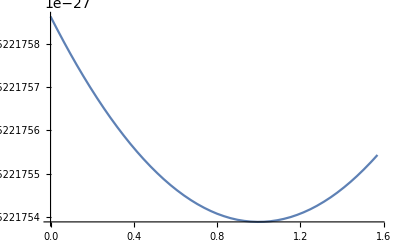

```mathematica
Plot[test2[x], {x,0, Pi/2}]
```

```mathematica
1000*^3*con
```

3.08568×10^24

```mathematica
intensity3[n0_,nc_] := 5.4*^-39*Integrate[(n0(d*Sec[theta])^-2.4+nc)^2d Sec[theta]^2, theta]
```

```mathematica
intensity3[0.001, 0.0005]
```

5.4×10^-39 d ((1.×10^-6 (AppellF1[0.5,-3.8,4.8,1.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]-2. AppellF1[0.5,-2.8,4.8,1.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]) Sin[theta])/(d^2 (d Sec[theta])^2.8 (1. AppellF1[0.5,-3.8,4.8,1.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]-2. AppellF1[0.5,-2.8,4.8,1.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]+(-3.2 AppellF1[1.5,-3.8,5.8,2.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]-2.53333 AppellF1[1.5,-2.8,4.8,2.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]+6.4 AppellF1[1.5,-2.8,5.8,2.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]+3.73333 AppellF1[1.5,-1.8,4.8,2.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]) Tan[0.5 theta]^2))+(1.×10^-6 (AppellF1[0.5,-1.4,2.4,1.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]-2. AppellF1[0.5,-0.4,2.4,1.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]) Sin[theta])/(d^2 (d Sec[theta])^0.4 (1. AppellF1[0.5,-1.4,2.4,1.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]-2. AppellF1[0.5,-0.4,2.4,1.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]+(-1.6 AppellF1[1.5,-1.4,3.4,2.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]-0.933333 AppellF1[1.5,-0.4,2.4,2.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]+3.2 AppellF1[1.5,-0.4,3.4,2.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]+0.533333 AppellF1[1.5,0.6,2.4,2.5,Tan[0.5 theta]^2,-1. Tan[0.5 theta]^2]) Tan[0.5 theta]^2))+2.5×10^-7 Tan[theta])

```mathematica
flux4[n0_,nc_,  D_, rStrom_, phi_] := 2*Pi*5.4*^-39*NIntegrate[(n0(D*Tan[phi]*Sec[theta])^-2.4+nc)^2D*Tan[phi]* Sec[theta]^2*Sin[phi]^2, {theta, 0, ArcCos[D*Tan[phi]/rStrom]}]/Sqrt[1*^7]
```

```mathematica
Table[{x,flux4[0.001, 0.0005, 200*^3*con,1000*^3*con, x]},{x,0.0001,ArcTan[1000/ 200],0.1}]
```

{{0.0001,8.27683×10^-32},{0.1001,8.26406×10^-26},{0.2001,3.26736×10^-25},{0.3001,7.21915×10^-25},{0.4001,1.25125×10^-24},{0.5001,1.89172×10^-24},{0.6001,2.61476×10^-24},{0.7001,3.38672×10^-24},{0.8001,4.16874×10^-24},{0.9001,4.91544×10^-24},{1.0001,5.56964×10^-24},{1.1001,6.04541×10^-24},{1.2001,6.16553×10^-24},{1.3001,5.32761×10^-24}}

```mathematica
test  = Interpolation[%]
```

InterpolatingFunction[{{0.0001, 1.3001}}, <>]

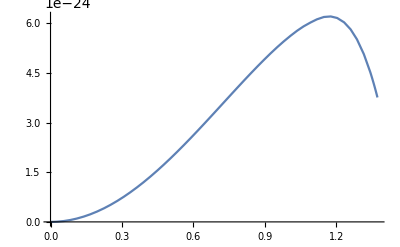

```mathematica
Plot[test[x],{x,0.0001,ArcTan[1000/ 200]}]
```

```mathematica
Integrate[test[x], {x,0.0001,ArcTan[1000/ 200]}]
```

InterpolatingFunction::dmvali: The integration endpoint ArcTan[5] in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

4.33266×10^-24

# Heating and cooling

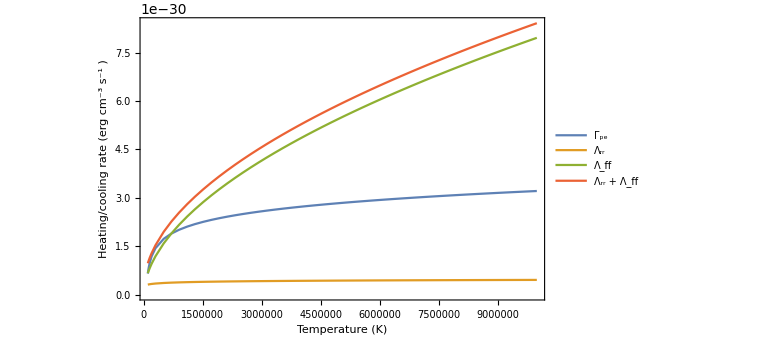

```mathematica
Plot[{(2.8214 - 2.18*^-11/(kcm*T))*alpha[T]*0.001^2*kcm*T,alpha[T]*0.001^2*(0.684-0.0416Log[T/1*^4])*kcm*T, alpha[T]*0.001^2*0.54*(T/1*^4)^0.37*kcm*T, alpha[T]*0.001^2*(0.684-0.0416Log[T/1*^4])*kcm*T+ alpha[T]*0.001^2*0.54*(T/1*^4)^0.37*kcm*T}, {T, 1*^5, 1*^7}, PlotLegends->LineLegend[Automatic,{Style[HoldForm[Subscript["Γ","pe"]]],Style[HoldForm[Subscript["Λ","rr"]]], Style[HoldForm[Subscript["Λ","ff"]]], Style[HoldForm[Subscript["Λ","rr"]"+"Subscript["Λ","ff"]]]}], LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["Heating/cooling rate (erg"Superscript["cm", -3]Superscript["s", -1]")"],18,FontFamily->"Arial"],None},{Style[HoldForm["Temperature (K)"],18,FontFamily->"Arial"],None}}]
```

```mathematica
Reduce[(2.8214 - 2.18*^-18/(kcm*T))*alpha[T]*0.001^2*kcm*T == alpha[T]*0.001^2*(0.684-0.0416Log[T/1*^4])*kcm*T+ alpha[T]*0.001^2*0.54*(T/1*^4)^0.37*kcm*T,T]//N
```

Reduce::inex: Reduce was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Reduce require exact input, providing Reduce with an exact version of the system may help.

Reduce[7.38453×10^-32 (2.8214-0.0157897/T) T^0.17==1.32043×10^-33 T^0.54+7.38453×10^-32 T^0.17 (0.684-0.0416 Log[0.0001 T]),T]

```mathematica
alpha[1*^6]*0.001^2*(0.684-0.0416Log[1*^6/1*^4])*kcm*1*^6
```

3.8077×10^-31

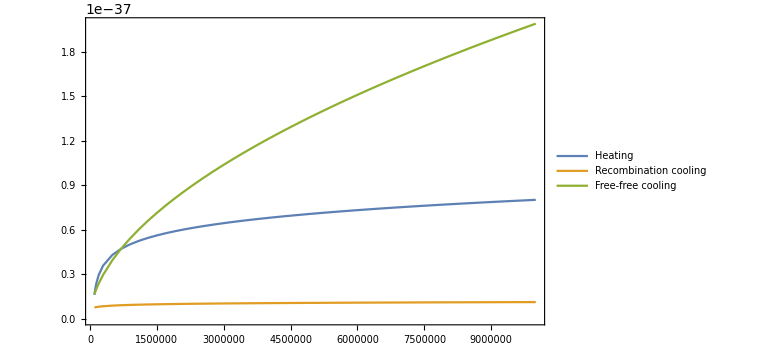

```mathematica
Plot[{(2.8214 - 2.18*^-18/(kmet*T))*alpha[T]*0.0005^2*kmet*T,alpha[T]*0.0005^2*(0.684-0.0416Log[T/1*^4])*kmet*T, alpha[T]*0.0005^2*0.54*(T/1*^4)^0.37*kmet*T}, {T, 1*^5, 1*^7}, PlotLegends->LineLegend[Automatic,{"Heating", "Recombination cooling", "Free-free cooling"}], LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->Thick, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["ν" Subscript["I","ν"] "(erg"Superscript["cm", -2]Superscript["s", -1]Superscript["str", -1]")"],18,FontFamily->"Arial"]}}]
```

# Front evolution

```mathematica
velocity[luminosity_,M_, rSource_, beta_,n0_,nc_,T0_,r_]:=Module[ {Q, rSourceCm, aMod, T, rCm, speed, soundspeed}, rSourceCm:= rSource*con;
rCm := r*con*1*^3+rSourceCm;
T:= 0.59*mP*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100); (*equation 23*)
Q:= luminosity*solarLum/(2.82*T*k); 
aMod :=2.56*^-13/(T/1*^4)^(0.833);
speed:=(Q/(4Pi(rCm-rSourceCm)^2(n0*rCm^-beta+nc)) - aMod*(n0*rCm^-beta+nc)(rCm-rSourceCm)/3 )/1*^3;
If[speed>3*^8, speed = 299792458, speed=speed];
soundspeed:= Sqrt[kmet/mP]*(Sqrt[2*T]+Sqrt[2*T-T0]);
If[speed<soundspeed, speed = soundspeed, speed=speed];
speed]
```

```mathematica
velocity[1.5*^10, 1*^12, 5*^4, 1.2, 0.001, 0.00003,1*^4, 800]
```

451680.

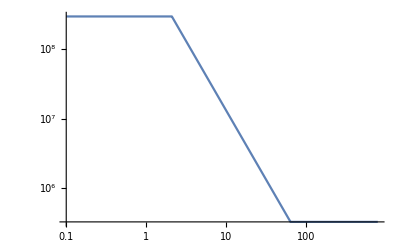

```mathematica
LogLogPlot[velocity[1.5*^10, 1*^12, 5*^4, 1.2, 0.001, 0.0003, 1*^4,r], {r, 0.1, 800}]
```

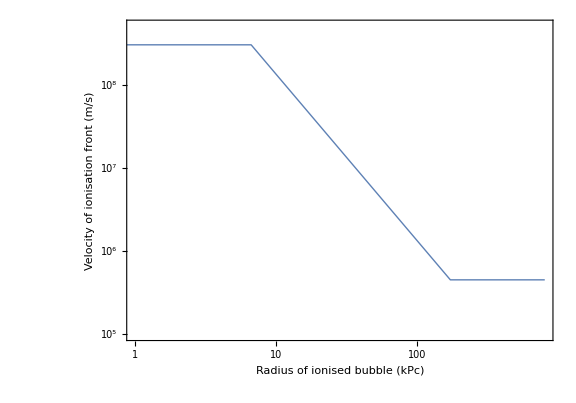

```mathematica
LogLogPlot[velocity[1.5*^10, 1*^12, 5*^4, 1.2, 0.001, 0.00003, 1*^4,r], {r, 0.1, 800}, PlotRange->{{1,800},{1*^5,5*^8}},    LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Directive[Thick]}, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style["Velocity of ionisation front (m/s)",18,FontFamily->"Arial"],None},{Style["Radius of ionised bubble (kPc)",18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]
```

```mathematica
timeSteps = Table[0.01*10*con/velocity[1.5*^10, 1*^12, 5*^4, 1.2, 0.001, 0.00003,1*^4, x], {x,0.1, 800, 0.01}];
```

```mathematica
timeVals = Accumulate[timeSteps]/(3600*24*365);
```

```mathematica
timeVals
```

{32.638,65.276,97.9139,130.552,163.19,195.828,228.466,261.104,293.742,326.38,359.018,391.656,424.294,456.932,79963,1.48506×10^9,1.48508×10^9,1.4851×10^9,1.48512×10^9,1.48514×10^9,1.48517×10^9,1.48519×10^9,1.48521×10^9,1.48523×10^9,1.48525×10^9,1.48527×10^9,1.4853×10^9,1.48532×10^9,1.48534×10^9}
 |  |  |  |

```mathematica
Last[timeVals]
```

1.6547×10^9

```mathematica
data = Transpose[{Table[x, {x,0.1, 800, 0.01}], timeVals}]
```

{{0.1,32.638},{0.11,65.276},{0.12,97.9139},{0.13,130.552},{0.14,163.19},{0.15,195.828},{0.16,228.466},{0.17,261.104},{0.18,293.742},79974,{799.93,1.48519×10^9},{799.94,1.48521×10^9},{799.95,1.48523×10^9},{799.96,1.48525×10^9},{799.97,1.48527×10^9},{799.98,1.4853×10^9},{799.99,1.48532×10^9},{800.,1.48534×10^9}}
 |  |  |  |

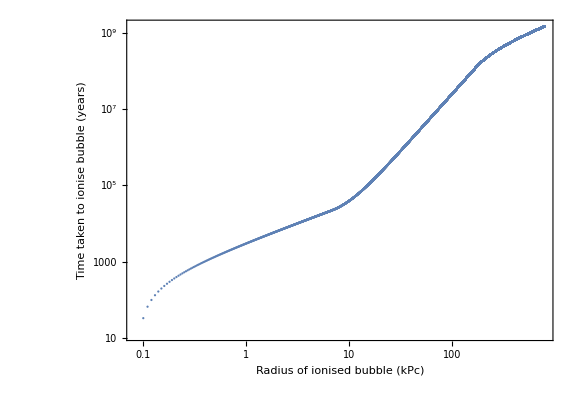

```mathematica
ListLogLogPlot[data,    LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],PlotStyle->{Directive[Thick]}, ImageSize->Large, Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.003],Black,18],FrameTicksStyle->Directive[Thickness[0.004]], FrameLabel->{{Style[HoldForm["Time taken to ionise bubble"" " "(years)"],18,FontFamily->"Arial"],None},{Style["Radius of ionised bubble (kPc)",18,FontFamily->"Arial"],None}},AspectRatio->.7,ImageSize->600]
```

```mathematica
tab = Table[x, {x,0.1, 800, 0.01}]
```

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,79953,799.82,799.83,799.84,799.85,799.86,799.87,799.88,799.89,799.9,799.91,799.92,799.93,799.94,799.95,799.96,799.97,799.98,799.99,800.}
 |  |  |  |

```mathematica
Plot[{Accumulate[timeSteps], Table[x, {x,0.1, 800, 0.01}]}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[{Accumulate[timeSteps],Table[x,{x,0.1,800,0.01}]}]

```mathematica
soundSpeedInside[T_]:= Sqrt[(5/3)*2*kmet*T/mP]
```

```mathematica
soundSpeedInside[1*^6]
```

165875.

```mathematica
soundSpeedOutside[T_]:= Sqrt[(5/3)*kmet*T/mP]
```

```mathematica
soundSpeedOutside[1*^4]
```

11729.2

```mathematica
rStag = 1000(8/3)^(2/3)(soundSpeedInside[1*^6]/soundSpeedOutside[1*^4])^(4/3)
```

65765.7

```mathematica
mStag = 4Pi*1000^3*^3*3*^16(8/3)^(8/3)(soundSpeedInside[1*^6]/soundSpeedOutside[1*^4])^(8/3)/3
```

2.00986310360908×10^9021

```mathematica
1000^3*^3*3*^16
```

30000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

# Psi

```mathematica
integral1[T_]:=Integrate[2*planck*v^3/(c^2*(Exp[planck*v/(k*T)]-1)), {v,0, Infinity}]
```

```mathematica
integral1[1*^6]
```

Integrate::idiv: Integral of (1.4745×10^-50 v^3)/(-1.+ⅇ^(7.68924×10^-36 v)) does not converge on {0,∞}.

∫_0^∞ (1.4745×10^-50 v^3)/(-1+ⅇ^(7.68924×10^-36 v))ⅆv

```mathematica
PlanckRadiationLaw[Quantity[1000000,"Kelvins"],Quantity[#,"Nanometers"]][[1]]&/@{100,200,300}
```

{7.6969×10^19,4.99×10^18,9.9768×10^17}

```mathematica
b[v_,t_]:= 2*h*v^3/(cs^2)(Exp[h*v/(kb*t)]-1)^-1
```

```mathematica
b2[v_,t_]:= 2*v^2*(h*v-h*v0)/(cs^2)(Exp[h*v/(kb*t)]-1)^-1
```

```mathematica
b3[v_,t_]:= 2h*v^3*(h*v-h*v0)/(cs^2)(Exp[h*v/(kb*t)]-1)^-1
```

```mathematica
D[b[v,t],v]
```

(6 h v^2)/(cs^2 (-1+ⅇ^((h v)/(kb t))))-(2 ⅇ^((h v)/(kb t)) h^2 v^3)/(cs^2 (-1+ⅇ^((h v)/(kb t)))^2 kb t)

```mathematica
Integrate[b[v,t], {v,0,Infinity}, Assumptions->Re[h/(kb*t)>0]]
```

```mathematica
Integrate[b2[v,t], {v,0,Infinity}, Assumptions->Re[h/(kb*t)>0]]
```

ConditionalExpression[(2 kb^3 t^3 (kb π^4 t-30 h v0 Zeta[3]))/(15 cs^2 h^3),Re[h/(kb t)]>0]

```mathematica
Zeta[5]
bUp[v_,t_]:= 2*v^2(h*v-h*v0)/(cs^2)(Exp[h*v/(kb*t)]-1)^-1;
```

Zeta[5]

```mathematica
Integrate[bUp[v,t], {v,0,Infinity}, Assumptions->Re[h/(kb*t)>0]]
```

ConditionalExpression[(2 kb^3 t^3 (kb π^4 t-30 h v0 Zeta[3]))/(15 cs^2 h^3),Re[h/(kb t)]>0]

```mathematica
bDown[v_,t_]:= 2*v^2/(cs^2)(Exp[h*v/(kb*t)]-1)^-1;
```

```mathematica
Integrate[bDown[v,t], {v,0,Infinity}, Assumptions->Re[h/(kb*t)>0]]
```

ConditionalExpression[(4 kb^3 t^3 Zeta[3])/(cs^2 h^3),Re[h/(kb t)]>0]

```mathematica
PlanckRadiationLaw[1*^6, 100]
```

PlanckRadiationLaw::notemp: 1000000 is not a recognized temperature specification.

PlanckRadiationLaw[1000000,100]

## 4 - Scrap code

```mathematica
temp3[luminosity_, M_, rSource_, beta_, n0_, nc_]:= Module[ {Q, rSourceCm, aMod, T}, rSourceCm:= rSource*con;
T:= 0.59*6.67408*^-11*M*solarMass/(2*1.38064852*^-23*rSourceCm/100); (*equation 23*)
Q:= luminosity*solarLum/(2.82*T*k); 
aMod:= 4.13*^-13*(T/1000)^(-0.7131); 
Q/(4*Pi*aMod)]
```

```mathematica
temp3[1.3*^10, 1*^12, 1*^5, 1.55, 0.001, 0.00001]
```

6.22633×10^58

```mathematica
Solve[0.001*0.341 == 1/(Sqrt[2Pi] *Exp[-(r-100)^/(2*
```

```mathematica
5.182053652856198*^27/con
```

1.67939×10^9

```mathematica
Solve[5.2160118247785535*^70==-4.43113462726379*^10-500000*ⅇ^(-x^2/10000000000) x+(4.43113462726379*^10)/x,{x,r}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[5.21601×10^70==-4.43113×10^10+(4.43113×10^10)/x-500000. ⅇ^(-x^2/10000000000) x,{x,r}]

```mathematica
rExpDec[luminosity_,temp_,rSource_,beta_,n0_, nc_]:= Module[{Q, rSourceCm}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*3.24078*^19;Solve[Q/(a*4*Pi)==n0/(3-beta)*(r^(3-beta)-rSourceCm^(3-beta))+nc/3*(r^3-rSourceCm^3),r]]
```

```mathematica
rExpDec[2*^10,1000,1*^5,1.5,0.01,0.000001]
```

{{r→-2.87705×10^24-4.9832×10^24 ⅈ},{r→-2.87705×10^24+4.9832×10^24 ⅈ},{r→5.75411×10^24}}

```mathematica
3.2897*^24/3.24078*^19
```

101510.

```mathematica
rGauss[luminosity_,temp_,rSource_,d_,n0_, nc_]:= Module[{Q, rSourceCm}, Q:= luminosity*solarLum/(2.82*temp*k); rSourceCm:= rSource*3.24078*^19;{Solve[Q/(a*4*Pi)-nc/3(r^3-rSourceCm^3)==Integrate[n0*x^2*Exp[-x^2/d^2],{x,rSourceCm,r}],r], rSource}]
```

```mathematica
rGauss[2*^10,1000,1*^5,1.5*^24,0.01,0.000001]
```

{{{r→-1.83057×10^26},{r→-1.30162×10^24},{r→1.84359×10^26}},100000}

## Temp modified

```mathematica
rExpDecT[luminosity_,rSource_,beta_,n0_, M_]:= Module[{Q, rSourceCm, T, aMod}, rSourceCm:= rSource*3.24078*^19; T:= 0.59*6.67408*^-11*M/(2*1.38064852*^-23*rSourceCm/100);
Q:= luminosity*solarLum/(2.82*T*k);
aMod:= 4.13*^-13*(T/0.0001)^(-0.7131); 
Solve[Q/(aMod*4*Pi)==n0/(3-beta)*(r^(3-beta)-rSourceCm^(3-beta))+nc/3*(r^3-rSourceCm^3),r]]
```

```mathematica
rExpDecT[2*^10,1*^12,1.5,0.001,1*^5]
```

rExpDecT[20000000000,1000000000000,1.5,0.001,100000]

## Temp modified non-fall off

```mathematica
rExpDecT[luminosity_,M_,rSource_,beta_,n0_, nc_]:= Module[{Q, rSourceCm, T, aMod, sol, realSol, DecSol, tv, s},rSourceCm:=rSource*3.24078*^19;  T:= 0.59*6.67408*^-11*M/(2*1.38064852*^-23*rSourceCm/100);Q:= luminosity*solarLum/(2.82*T*k);
aMod:= 4.13*^13*(T/0.0001)^(-0.7131); 
test:=Solve[T == r^2 - rSourceCm^2+r^3-rSourceCm^3, r];
sol:= Solve[Q/(1*^13*4*Pi)==n0/(3-beta)*(r^(3-beta)-rSourceCm^(3-beta))+nc/3*(r^3-rSourceCm^3),r];  realSol := Cases[sol,_?(FreeQ[N[#,16],Complex]&)]; {test,sol}]
```

```mathematica
r/.rExpDecT[2*^10,1*^12,1*^5,1.5,0.01,0.1][[1]]
DecSol= r/.Select[realSol, (r/.#)>0&][[1]]; {sol, DecSol/3.24078*^19}
```

{-1.62039×10^24-2.8066×10^24 ⅈ,-1.62039×10^24+2.8066×10^24 ⅈ,3.24078×10^24}

Select::normal: Nonatomic expression expected at position 1 in Select[realSol,(r/.#1)>0&].

ReplaceAll::reps: {realSol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{sol,3.08568×10^-20 (r/.realSol)}

```mathematica
test2[tv_]:=  Solve[tv^-0.7 ==s^2-tv^2+s^3-tv^3, s]
```

```mathematica
test2[7]
```

{{s→-4.0008-6.32594 ⅈ},{s→-4.0008+6.32594 ⅈ},{s→7.00159}}

```mathematica
563^-0.713
```

0.0109367

```mathematica
rExpDecT[2,0.005,1*^5,1,0.01,0.01]
```

{{{r→-1.62039×10^24-2.8066×10^24 ⅈ},{r→-1.62039×10^24+2.8066×10^24 ⅈ},{r→3.24078×10^24}},{{r→-1.62039×10^24-2.8066×10^24 ⅈ},{r→-1.62039×10^24+2.8066×10^24 ⅈ},{r→3.24078×10^24}}}

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[temp]

```mathematica
rGaussT[luminosity_,M_,rSource_,d_,n0_, nc_]:= Module[{Q, rSourceCm, aMod, T},  rSourceCm:= rSource*3.24078*^19; T:= 0.59*6.67408*^-11*M/(2*1.38064852*^-23*rSourceCm/100);Q:= luminosity*solarLum/(2.82*T*k);
aMod:= 4.13*^13*(T/0.0001)^(-0.7131); 
 Solve[Q/(aMod*4*Pi)-nc/3(r^3-rSourceCm^3)==Integrate[n0*x^2*Exp[-x^2/d^2],{x,rSourceCm,r}],r]]
```

```mathematica
SolrGaussT = rGaussT[2*^10,1*^12,2*^4,1.5*^15,0.001,0.00001]
```

{{r→-3.24078×10^23-5.6132×10^23 ⅈ},{r→-3.24078×10^23+5.6132×10^23 ⅈ},{r→6.48156×10^23}}

```mathematica
ReSolExpDecT = Cases[SolrGaussT,_?(FreeQ[N[#,16],Complex]&)]

Cases[SolrGaussT,_?(FreeQ[N[#,16],Real]&)]
```

{{r→6.48156×10^23}}

{{r→-3.24078×10^23-5.6132×10^23 ⅈ},{r→-3.24078×10^23+5.6132×10^23 ⅈ},{r→6.48156×10^23}}

```mathematica
Select[SolrGaussT, (r/.#)>0&]
```

Select::normal: Nonatomic expression expected at position 1 in Select[SolrGaussT,(r/.#1)>0&].

Select[SolrGaussT,(r/.#1)>0&]

## Visualisation Milky Way

```mathematica
17563.695
```

17563.7

```mathematica
1.53122*^25/3.24078*^19
```

472485.

```mathematica
5.87371*^25/3.24078*^19
```

1.81244×10^6

```mathematica
spheres=Graphics3D[{Opacity[0.3,Black],Sphere[{0,0,0},1],Red,Sphere[{0,0,0},1.7564],Blue,Sphere[{0,0,0},49.6235],Green,Sphere[{0,0,0},190.354], Circle[{0,0}, 10]},Axes -> True,AxesLabel -> {"x","y","z"}]
```

-Graphics3D-

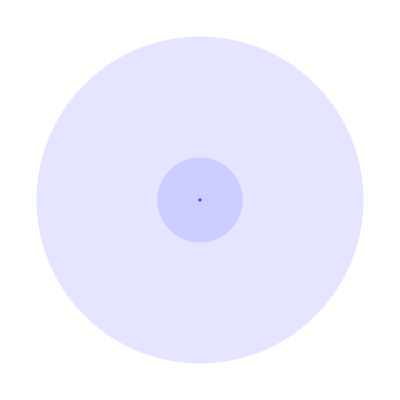

```mathematica
Graphics[{Opacity[0.5], Black,Disk[{0,0},100], Blue,Disk[{0,0},476.244],Opacity[0.1] ,Disk[{0,0},2], Disk[{0,0},49.6235], Disk[{0,0},190.354], Dashed,Circle[{0,0},2], Red,Disk[{7.5,0}]}]
```

```mathematica
temp[rSourceCm1_]:= Solve[100==(b^(1.5)-rSourceCm1^(1.5))+b^1.5-rSourceCm1^1.5,b]
```

```mathematica
temp[20]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{b→26.8904}}

```mathematica
Style[#,FontFamily->#]&/@$FontFamilies
```